# Fix small growth noise, vary measurement noise

```mathematica
αtf = 0.005
```

0.005

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP= λt*D[yt*P[xt, yt], xt]+D[yt*P[xt, yt], yt]-D[xt*P[xt, yt],yt]+(αt^2/2)D[P[xt, yt],{xt,2}]+(αtv^2/2)D[P[xt, yt],{yt,2}]/.{αt->αtf}
```

P[xt,yt]-xt P^(0,1)[xt,yt]+yt P^(0,1)[xt,yt]+1/2 αtv^2 P^(0,2)[xt,yt]+yt λt P^(1,0)[xt,yt]+0.0000125 P^(2,0)[xt,yt]

## Get the steady-state variances

```mathematica
A= {{ 0,λt},{-1, 1}}
B = {{αtf,0},{0,αtv}}
s=Array[Y,{2,2}]
ss =( s/. Expand[FullSimplify[Solve[A.s+s.Transpose[A]==B.Transpose[B], Flatten[s]]]])[[1]]
```

{{0,λt},{-1,1}}

{{0.005,0},{0,αtv}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{0.0000125+0.0000125/λt+0.5 αtv^2 λt,0.0000125/λt},{0.0000125/λt,0.5 αtv^2+0.0000125/λt}}

```mathematica
Eigenvectors[A]
```

{{1/2 (1+√(1-4 λt)),1},{1/2 (1-√(1-4 λt)),1}}

```mathematica
small = Eigenvalues[ss][[1]]
```

1/λt 0.5 (0.000025+0.0000125 λt+0.5 αtv^2 λt+0.5 αtv^2 λt^2-√(6.25×10^-10+1.5625×10^-10 λt^2-0.0000125 αtv^2 λt^2+0.25 αtv^4 λt^2+0.0000125 αtv^2 λt^3-0.5 αtv^4 λt^3+0.25 αtv^4 λt^4))

```mathematica
minSizes = Table[Sqrt[small]/.p, {p, params}]
```

{0.00353642,0.00559115,0.00790294,0.0102956,0.0248315,0.0365501,0.0475701,0.0035373,0.00559214,0.00790022,0.0102835,0.0245371,0.0355112,0.0450995,0.00353995,0.00559514,0.00789221,0.0102475,0.0236578,0.0325215,0.038684,0.00354216,0.00559769,0.00788572,0.010218,0.0229437,0.0303288,0.0347536,0.00354436,0.00560028,0.00787942,0.0101889,0.0222599,0.0284639,0.0318446,0.00354877,0.00560557,0.00786735,0.0101321,0.0210141,0.025608,0.0279879,0.00355317,0.00561103,0.00785601,0.0100773,0.0199505,0.0236239,0.0256679}

## Choose the parameter values

```mathematica
λts = {0.001, 0.002, 0.005, 0.0075, 0.01, 0.015, 0.02};
αtvs = {0.005, 0.01,0.015, 0.02, 0.05,0.075, 0.1};
αArray2 = Flatten[Table[{αtvs },7]]^2
params = Flatten[Table[{λt->l, αtv->a}, {l, λts}, {a, αtvs}], 1]
legend =  Flatten[Table["λt="<>ToString[l]<>"; "<> "αtv="<>ToString[a], {l, λts},{a, αtvs}], 1];
```

{0.000025,0.0001,0.000225,0.0004,0.0025,0.005625,0.01,0.000025,0.0001,0.000225,0.0004,0.0025,0.005625,0.01,0.000025,0.0001,0.000225,0.0004,0.0025,0.005625,0.01,0.000025,0.0001,0.000225,0.0004,0.0025,0.005625,0.01,0.000025,0.0001,0.000225,0.0004,0.0025,0.005625,0.01,0.000025,0.0001,0.000225,0.0004,0.0025,0.005625,0.01,0.000025,0.0001,0.000225,0.0004,0.0025,0.005625,0.01}

{{λt→0.001,αtv→0.005},{λt→0.001,αtv→0.01},{λt→0.001,αtv→0.015},{λt→0.001,αtv→0.02},{λt→0.001,αtv→0.05},{λt→0.001,αtv→0.075},{λt→0.001,αtv→0.1},{λt→0.002,αtv→0.005},{λt→0.002,αtv→0.01},{λt→0.002,αtv→0.015},{λt→0.002,αtv→0.02},{λt→0.002,αtv→0.05},{λt→0.002,αtv→0.075},{λt→0.002,αtv→0.1},{λt→0.005,αtv→0.005},{λt→0.005,αtv→0.01},{λt→0.005,αtv→0.015},{λt→0.005,αtv→0.02},{λt→0.005,αtv→0.05},{λt→0.005,αtv→0.075},{λt→0.005,αtv→0.1},{λt→0.0075,αtv→0.005},{λt→0.0075,αtv→0.01},{λt→0.0075,αtv→0.015},{λt→0.0075,αtv→0.02},{λt→0.0075,αtv→0.05},{λt→0.0075,αtv→0.075},{λt→0.0075,αtv→0.1},{λt→0.01,αtv→0.005},{λt→0.01,αtv→0.01},{λt→0.01,αtv→0.015},{λt→0.01,αtv→0.02},{λt→0.01,αtv→0.05},{λt→0.01,αtv→0.075},{λt→0.01,αtv→0.1},{λt→0.015,αtv→0.005},{λt→0.015,αtv→0.01},{λt→0.015,αtv→0.015},{λt→0.015,αtv→0.02},{λt→0.015,αtv→0.05},{λt→0.015,αtv→0.075},{λt→0.015,αtv→0.1},{λt→0.02,αtv→0.005},{λt→0.02,αtv→0.01},{λt→0.02,αtv→0.015},{λt→0.02,αtv→0.02},{λt→0.02,αtv→0.05},{λt→0.02,αtv→0.075},{λt→0.02,αtv→0.1}}

## Get the trajectory of the mean

```mathematica
eig=FullSimplify[Eigenvectors[A]]
```

{{1/2 (1+√(1-4 λt)),1},{1/2 (1-√(1-4 λt)),1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1-√(1-4 λt)),1/2 (1+√(1-4 λt))}

```mathematica
cs =Re[N[ Flatten[Table[(eig[[1,1]])^-1/.p, {p, params}]]]]
```

{1.001,1.001,1.001,1.001,1.001,1.001,1.001,1.00201,1.00201,1.00201,1.00201,1.00201,1.00201,1.00201,1.00505,1.00505,1.00505,1.00505,1.00505,1.00505,1.00505,1.00761,1.00761,1.00761,1.00761,1.00761,1.00761,1.00761,1.01021,1.01021,1.01021,1.01021,1.01021,1.01021,1.01021,1.01547,1.01547,1.01547,1.01547,1.01547,1.01547,1.01547,1.02084,1.02084,1.02084,1.02084,1.02084,1.02084,1.02084}

## Set up the mesh, boundary conditions, and initial condition

#### Steady-state distribution widths in x~, y~

```mathematica
xtwidths = N[Table[ss[[1,1]]/.p, {p, params}]];
ytwidths = N[Table[ss[[2,2]]/.p, {p, params}]];
xywidths =  N[Table[ss[[1,2]]/.p, {p, params}]];
xtStds =Sqrt[xtwidths]
ytStds = Sqrt[ytwidths]
covStds = Sqrt[xywidths]
```

{0.111859,0.11186,0.11186,0.11186,0.111865,0.111872,0.111882,0.0791361,0.0791366,0.0791374,0.0791385,0.0791518,0.0791715,0.0791991,0.0501255,0.0501273,0.0501305,0.0501348,0.0501871,0.0502649,0.0503736,0.0409788,0.0409822,0.0409879,0.0409959,0.0410919,0.0412342,0.0414327,0.0355334,0.0355387,0.0355475,0.0355598,0.0357071,0.0359253,0.0362284,0.0290864,0.0290961,0.0291122,0.0291347,0.0294038,0.0297997,0.0303452,0.0252537,0.0252686,0.0252933,0.0253279,0.0257391,0.0263391,0.027157}

{0.111859,0.112027,0.112305,0.112694,0.11726,0.123744,0.132288,0.079136,0.0793725,0.0797653,0.0803119,0.0866025,0.0951972,0.106066,0.0501248,0.0504975,0.0511126,0.0519615,0.0612372,0.0728869,0.0866025,0.0409776,0.0414327,0.0421802,0.0432049,0.0540062,0.0669266,0.0816497,0.0355317,0.0360555,0.0369121,0.0380789,0.05,0.0637377,0.0790569,0.0290832,0.0297209,0.0307544,0.0321455,0.0456435,0.0603807,0.0763763,0.0252488,0.0259808,0.027157,0.0287228,0.0433013,0.0586302,0.075}

{0.111803,0.111803,0.111803,0.111803,0.111803,0.111803,0.111803,0.0790569,0.0790569,0.0790569,0.0790569,0.0790569,0.0790569,0.0790569,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.0408248,0.0408248,0.0408248,0.0408248,0.0408248,0.0408248,0.0408248,0.0353553,0.0353553,0.0353553,0.0353553,0.0353553,0.0353553,0.0353553,0.0288675,0.0288675,0.0288675,0.0288675,0.0288675,0.0288675,0.0288675,0.025,0.025,0.025,0.025,0.025,0.025,0.025}

```mathematica
θs = ArcTan[cs]
yt0 = 1+5*ytStds
xt0 = yt0/cs
```

{0.785899,0.785899,0.785899,0.785899,0.785899,0.785899,0.785899,0.786401,0.786401,0.786401,0.786401,0.786401,0.786401,0.786401,0.787917,0.787917,0.787917,0.787917,0.787917,0.787917,0.787917,0.789191,0.789191,0.789191,0.789191,0.789191,0.789191,0.789191,0.790475,0.790475,0.790475,0.790475,0.790475,0.790475,0.790475,0.793072,0.793072,0.793072,0.793072,0.793072,0.793072,0.793072,0.795712,0.795712,0.795712,0.795712,0.795712,0.795712,0.795712}

{1.5593,1.56013,1.56153,1.56347,1.5863,1.61872,1.66144,1.39568,1.39686,1.39883,1.40156,1.43301,1.47599,1.53033,1.25062,1.25249,1.25556,1.25981,1.30619,1.36443,1.43301,1.20489,1.20716,1.2109,1.21602,1.27003,1.33463,1.40825,1.17766,1.18028,1.18456,1.19039,1.25,1.31869,1.39528,1.14542,1.1486,1.15377,1.16073,1.22822,1.3019,1.38188,1.12624,1.1299,1.13578,1.14361,1.21651,1.29315,1.375}

{1.55774,1.55857,1.55996,1.56191,1.58471,1.6171,1.65977,1.39288,1.39406,1.39602,1.39875,1.43014,1.47303,1.52726,1.24434,1.24619,1.24925,1.25348,1.29962,1.35758,1.42581,1.19578,1.19804,1.20175,1.20684,1.26043,1.32455,1.39761,1.16576,1.16835,1.17259,1.17837,1.23737,1.30537,1.38119,1.12797,1.13111,1.1362,1.14305,1.20951,1.28207,1.36083,1.10325,1.10683,1.1126,1.12027,1.19167,1.26675,1.34693}

```mathematica
Δx = 5*xtStds
Δy =5*ytStds
lrange =Flatten[Transpose[Table[λts,7]]]
ΩFunc[Δx_, Δy_, λ_, xt0_, yt0_] :=Parallelogram[{1/2 (1+√(1-4 λ))-Δx, 1}, {{2Δx, 0}, {(yt0-1+Δy)*(1/2 (1+√(1-4 λ))),(yt0-1+Δy)}}]
Ω=MapThread[ΩFunc,{Δx, Δy, lrange,xt0,yt0}];
```

{0.559297,0.559298,0.559299,0.559301,0.559324,0.559359,0.559408,0.395681,0.395683,0.395687,0.395692,0.395759,0.395857,0.395996,0.250627,0.250637,0.250652,0.250674,0.250936,0.251325,0.251868,0.204894,0.204911,0.20494,0.20498,0.205459,0.206171,0.207163,0.177667,0.177694,0.177738,0.177799,0.178536,0.179626,0.181142,0.145432,0.145481,0.145561,0.145674,0.147019,0.148998,0.151726,0.126269,0.126343,0.126466,0.126639,0.128695,0.131696,0.135785}

{0.559296,0.560134,0.561527,0.563471,0.586302,0.618718,0.661438,0.39568,0.396863,0.398826,0.401559,0.433013,0.475986,0.53033,0.250624,0.252488,0.255563,0.259808,0.306186,0.364434,0.433013,0.204888,0.207163,0.210901,0.216025,0.270031,0.334633,0.408248,0.177658,0.180278,0.18456,0.190394,0.25,0.318689,0.395285,0.145416,0.148605,0.153772,0.160728,0.228218,0.301904,0.381881,0.126244,0.129904,0.135785,0.143614,0.216506,0.293151,0.375}

{0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.005,0.005,0.005,0.005,0.005,0.005,0.005,0.0075,0.0075,0.0075,0.0075,0.0075,0.0075,0.0075,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.02,0.02,0.02,0.02,0.02,0.02,0.02}

```mathematica
Ω[[1]]
```

Parallelogram[{0.439702,1},{{1.11859,0},{1.11747,1.11859}}]

```mathematica
maxCell =minSizes/2
```

{0.00176821,0.00279558,0.00395147,0.0051478,0.0124157,0.018275,0.023785,0.00176865,0.00279607,0.00395011,0.00514174,0.0122686,0.0177556,0.0225497,0.00176998,0.00279757,0.0039461,0.00512376,0.0118289,0.0162608,0.019342,0.00177108,0.00279884,0.00394286,0.00510899,0.0114719,0.0151644,0.0173768,0.00177218,0.00280014,0.00393971,0.00509445,0.0111299,0.014232,0.0159223,0.00177438,0.00280279,0.00393368,0.00506605,0.010507,0.012804,0.0139939,0.00177658,0.00280551,0.00392801,0.00503864,0.00997527,0.0118119,0.012834}

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
meshes = MapThread[ToElementMesh[#1, MaxCellMeasure->{"Length"->#2}, "MaxBoundaryCellMeasure"->#2/4]&, {Ω, maxCell}]
```

{ElementMesh[{{0.439702,2.67577},{1.,2.11859}},{TriangleElement[<2952640>]}],ElementMesh[{{0.439701,2.67744},{1.,2.12027}},{TriangleElement[<1185548>]}],ElementMesh[{{0.4397,2.68023},{1.,2.12305}},{TriangleElement[<597846>]}],ElementMesh[{{0.439698,2.68411},{1.,2.12694}},{TriangleElement[<356986>]}],ElementMesh[{{0.439675,2.72975},{1.,2.1726}},{TriangleElement[<66014>]}],ElementMesh[{{0.43964,2.79456},{1.,2.23744}},{TriangleElement[<33288>]}],ElementMesh[{{0.439591,2.87996},{1.,2.32288}},{TriangleElement[<21276>]}],ElementMesh[{{0.602315,2.18345},{1.,1.79136}},{TriangleElement[<1483648>]}],ElementMesh[{{0.602313,2.18581},{1.,1.79373}},{TriangleElement[<597812>]}],ElementMesh[{{0.602309,2.18974},{1.,1.79765}},{TriangleElement[<303518>]}],ElementMesh[{{0.602304,2.1952},{1.,1.80312}},{TriangleElement[<182198>]}],ElementMesh[{{0.602237,2.25804},{1.,1.86603}},{TriangleElement[<36134>]}],ElementMesh[{{0.602139,2.34392},{1.,1.95197}},{TriangleElement[<19536>]}],ElementMesh[{{0.602,2.45253},{1.,2.06066}},{TriangleElement[<13842>]}],ElementMesh[{{0.744347,1.74433},{1.,1.50125}},{TriangleElement[<598358>]}],ElementMesh[{{0.744338,1.74805},{1.,1.50498}},{TriangleElement[<243614>]}],ElementMesh[{{0.744322,1.75418},{1.,1.51113}},{TriangleElement[<125376>]}],ElementMesh[{{0.744301,1.76265},{1.,1.51962}},{TriangleElement[<76782>]}],ElementMesh[{{0.744039,1.85521},{1.,1.61237}},{TriangleElement[<17952>]}],ElementMesh[{{0.74365,1.97151},{1.,1.72887}},{TriangleElement[<11724>]}],ElementMesh[{{0.743107,2.10852},{1.,1.86603}},{TriangleElement[<10070>]}],ElementMesh[{{0.787549,1.60402},{1.,1.40978}},{TriangleElement[<401272>]}],ElementMesh[{{0.787532,1.60855},{1.,1.41433}},{TriangleElement[<164344>]}],ElementMesh[{{0.787503,1.616},{1.,1.4218}},{TriangleElement[<85632>]}],ElementMesh[{{0.787463,1.62621},{1.,1.43205}},{TriangleElement[<52854>]}],ElementMesh[{{0.786984,1.73388},{1.,1.54006}},{TriangleElement[<13978>]}],ElementMesh[{{0.786272,1.86282},{1.,1.66927}},{TriangleElement[<10278>]}],ElementMesh[{{0.78528,2.00993},{1.,1.8165}},{TriangleElement[<9686>]}],ElementMesh[{{0.812231,1.51929},{1.,1.35532}},{TriangleElement[<302330>]}],ElementMesh[{{0.812204,1.5245},{1.,1.36056}},{TriangleElement[<124464>]}],ElementMesh[{{0.81216,1.53303},{1.,1.36912}},{TriangleElement[<65560>]}],ElementMesh[{{0.812099,1.54464},{1.,1.38079}},{TriangleElement[<41080>]}],ElementMesh[{{0.811362,1.66338},{1.,1.5}},{TriangleElement[<12170>]}],ElementMesh[{{0.810272,1.80046},{1.,1.63738}},{TriangleElement[<9814>]}],ElementMesh[{{0.808756,1.95362},{1.,1.79057}},{TriangleElement[<9822>]}],ElementMesh[{{0.839336,1.4166},{1.,1.29083}},{TriangleElement[<202810>]}],ElementMesh[{{0.839287,1.42293},{1.,1.29721}},{TriangleElement[<84640>]}],ElementMesh[{{0.839207,1.43319},{1.,1.30754}},{TriangleElement[<45380>]}],ElementMesh[{{0.839094,1.447},{1.,1.32146}},{TriangleElement[<29286>]}],ElementMesh[{{0.837749,1.58127},{1.,1.45644}},{TriangleElement[<10336>]}],ElementMesh[{{0.83577,1.72838},{1.,1.60381}},{TriangleElement[<9552>]}],ElementMesh[{{0.833042,1.88862},{1.,1.76376}},{TriangleElement[<10286>]}],ElementMesh[{{0.853315,1.35318},{1.,1.25249}},{TriangleElement[<153460>]}],ElementMesh[{{0.85324,1.36043},{1.,1.25981}},{TriangleElement[<64556>]}],ElementMesh[{{0.853117,1.37207},{1.,1.27157}},{TriangleElement[<35206>]}],ElementMesh[{{0.852944,1.38759},{1.,1.28723}},{TriangleElement[<23188>]}],ElementMesh[{{0.850888,1.53245},{1.,1.43301}},{TriangleElement[<9646>]}],ElementMesh[{{0.847887,1.68561},{1.,1.5863}},{TriangleElement[<9584>]}],ElementMesh[{{0.843798,1.85006},{1.,1.75}},{TriangleElement[<10814>]}]}

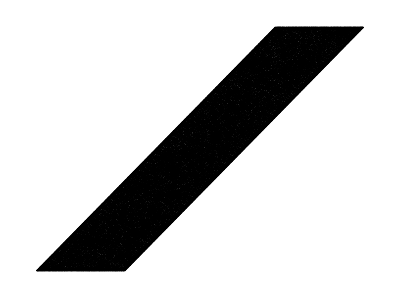

```mathematica
meshes[[49]]["Wireframe"]
```

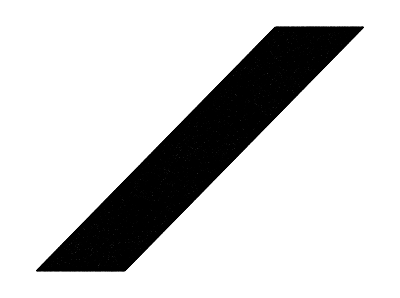

```mathematica
meshes[[49]]["Wireframe"]
```

```mathematica
bcs=Table[DirichletCondition[P[xt,yt]==0,ElementMarker==#]&/@m["BoundaryElementMarkerUnion"], {m, meshes}];
```

```mathematica
icPos =Transpose[{xt0, yt0}]
icVar =Table[ss/.p, {p, params}]
ic0 = N[MapThread[PDF[MultinormalDistribution[#1,#2], {xt, yt}]&, {icPos, icVar}]]
```

{{1.55774,1.5593},{1.55857,1.56013},{1.55996,1.56153},{1.56191,1.56347},{1.58471,1.5863},{1.6171,1.61872},{1.65977,1.66144},{1.39288,1.39568},{1.39406,1.39686},{1.39602,1.39883},{1.39875,1.40156},{1.43014,1.43301},{1.47303,1.47599},{1.52726,1.53033},{1.24434,1.25062},{1.24619,1.25249},{1.24925,1.25556},{1.25348,1.25981},{1.29962,1.30619},{1.35758,1.36443},{1.42581,1.43301},{1.19578,1.20489},{1.19804,1.20716},{1.20175,1.2109},{1.20684,1.21602},{1.26043,1.27003},{1.32455,1.33463},{1.39761,1.40825},{1.16576,1.17766},{1.16835,1.18028},{1.17259,1.18456},{1.17837,1.19039},{1.23737,1.25},{1.30537,1.31869},{1.38119,1.39528},{1.12797,1.14542},{1.13111,1.1486},{1.1362,1.15377},{1.14305,1.16073},{1.20951,1.22822},{1.28207,1.3019},{1.36083,1.38188},{1.10325,1.12624},{1.10683,1.1299},{1.1126,1.13578},{1.12027,1.14361},{1.19167,1.21651},{1.26675,1.29315},{1.34693,1.375}}

{{{0.0125125,0.0125},{0.0125,0.0125125}},{{0.0125126,0.0125},{0.0125,0.01255}},{{0.0125126,0.0125},{0.0125,0.0126125}},{{0.0125127,0.0125},{0.0125,0.0127}},{{0.0125138,0.0125},{0.0125,0.01375}},{{0.0125153,0.0125},{0.0125,0.0153125}},{{0.0125175,0.0125},{0.0125,0.0175}},{{0.00626253,0.00625},{0.00625,0.0062625}},{{0.0062626,0.00625},{0.00625,0.0063}},{{0.00626273,0.00625},{0.00625,0.0063625}},{{0.0062629,0.00625},{0.00625,0.00645}},{{0.006265,0.00625},{0.00625,0.0075}},{{0.00626813,0.00625},{0.00625,0.0090625}},{{0.0062725,0.00625},{0.00625,0.01125}},{{0.00251256,0.0025},{0.0025,0.0025125}},{{0.00251275,0.0025},{0.0025,0.00255}},{{0.00251306,0.0025},{0.0025,0.0026125}},{{0.0025135,0.0025},{0.0025,0.0027}},{{0.00251875,0.0025},{0.0025,0.00375}},{{0.00252656,0.0025},{0.0025,0.0053125}},{{0.0025375,0.0025},{0.0025,0.0075}},{{0.00167926,0.00166667},{0.00166667,0.00167917}},{{0.00167954,0.00166667},{0.00166667,0.00171667}},{{0.00168001,0.00166667},{0.00166667,0.00177917}},{{0.00168067,0.00166667},{0.00166667,0.00186667}},{{0.00168854,0.00166667},{0.00166667,0.00291667}},{{0.00170026,0.00166667},{0.00166667,0.00447917}},{{0.00171667,0.00166667},{0.00166667,0.00666667}},{{0.00126262,0.00125},{0.00125,0.0012625}},{{0.001263,0.00125},{0.00125,0.0013}},{{0.00126363,0.00125},{0.00125,0.0013625}},{{0.0012645,0.00125},{0.00125,0.00145}},{{0.001275,0.00125},{0.00125,0.0025}},{{0.00129062,0.00125},{0.00125,0.0040625}},{{0.0013125,0.00125},{0.00125,0.00625}},{{0.000846021,0.000833333},{0.000833333,0.000845833}},{{0.000846583,0.000833333},{0.000833333,0.000883333}},{{0.000847521,0.000833333},{0.000833333,0.000945833}},{{0.000848833,0.000833333},{0.000833333,0.00103333}},{{0.000864583,0.000833333},{0.000833333,0.00208333}},{{0.000888021,0.000833333},{0.000833333,0.00364583}},{{0.000920833,0.000833333},{0.000833333,0.00583333}},{{0.00063775,0.000625},{0.000625,0.0006375}},{{0.0006385,0.000625},{0.000625,0.000675}},{{0.00063975,0.000625},{0.000625,0.0007375}},{{0.0006415,0.000625},{0.000625,0.000825}},{{0.0006625,0.000625},{0.000625,0.001875}},{{0.00069375,0.000625},{0.000625,0.0034375}},{{0.0007375,0.000625},{0.000625,0.005625}}}

{284.563 2.71828^(0.5 (-1. (-1.55774+xt) (40000. (-1.55774+xt)-39960. (-1.5593+yt))-1. (-39960. (-1.55774+xt)+40000. (-1.5593+yt)) (-1.5593+yt))),179.919 2.71828^(0.5 (-1. (-1.55857+xt) (16038.3 (-1.55857+xt)-15974.4 (-1.56013+yt))-1. (-15974.4 (-1.55857+xt)+15990.4 (-1.56013+yt)) (-1.56013+yt))),127.209 2.71828^(0.5 (-1. (-1.55996+xt) (8057.43 (-1.55996+xt)-7985.56 (-1.56153+yt))-1. (-7985.56 (-1.55996+xt)+7993.62 (-1.56153+yt)) (-1.56153+yt))),97.5605 2.71828^(0.5 (-1. (-1.56191+xt) (4772.12 (-1.56191+xt)-4696.97 (-1.56347+yt))-1. (-4696.97 (-1.56191+xt)+4701.74 (-1.56347+yt)) (-1.56347+yt))),40.022 2.71828^(0.5 (-1. (-1.58471+xt) (869.479 (-1.58471+xt)-790.436 (-1.5863+yt))-1. (-790.436 (-1.58471+xt)+791.305 (-1.5863+yt)) (-1.5863+yt))),26.7532 2.71828^(0.5 (-1. (-1.6171+xt) (432.67 (-1.6171+xt)-353.2 (-1.61872+yt))-1. (-353.2 (-1.6171+xt)+353.633 (-1.61872+yt)) (-1.61872+yt))),20.0825 2.71828^(0.5 (-1. (-1.65977+xt) (278.635 (-1.65977+xt)-199.025 (-1.66144+yt))-1. (-199.025 (-1.65977+xt)+199.303 (-1.66144+yt)) (-1.66144+yt))),402.231 2.71828^(0.5 (-1. (-1.39288+xt) (39999.9 (-1.39288+xt)-39920.1 (-1.39568+yt))-1. (-39920.1 (-1.39288+xt)+40000.1 (-1.39568+yt)) (-1.39568+yt))),254.24 2.71828^(0.5 (-1. (-1.39406+xt) (16076.3 (-1.39406+xt)-15948.8 (-1.39686+yt))-1. (-15948.8 (-1.39406+xt)+15980.9 (-1.39686+yt)) (-1.39686+yt))),179.737 2.71828^(0.5 (-1. (-1.39602+xt) (8114.52 (-1.39602+xt)-7971.05 (-1.39883+yt))-1. (-7971.05 (-1.39602+xt)+7987.28 (-1.39883+yt)) (-1.39883+yt))),137.839 2.71828^(0.5 (-1. (-1.39875+xt) (4837.97 (-1.39875+xt)-4687.95 (-1.40156+yt))-1. (-4687.95 (-1.39875+xt)+4697.63 (-1.40156+yt)) (-1.40156+yt))),56.5354 2.71828^(0.5 (-1. (-1.43014+xt) (946.372 (-1.43014+xt)-788.644 (-1.43301+yt))-1. (-788.644 (-1.43014+xt)+790.536 (-1.43301+yt)) (-1.43301+yt))),37.7845 2.71828^(0.5 (-1. (-1.47303+xt) (510.783 (-1.47303+xt)-352.264 (-1.47599+yt))-1. (-352.264 (-1.47303+xt)+353.285 (-1.47599+yt)) (-1.47599+yt))),28.3559 2.71828^(0.5 (-1. (-1.52726+xt) (357.107 (-1.52726+xt)-198.393 (-1.53033+yt))-1. (-198.393 (-1.52726+xt)+199.107 (-1.53033+yt)) (-1.53033+yt))),635.03 2.71828^(0.5 (-1. (-1.24434+xt) (39999.5 (-1.24434+xt)-39800.5 (-1.25062+yt))-1. (-39800.5 (-1.24434+xt)+40000.5 (-1.25062+yt)) (-1.25062+yt))),401.017 2.71828^(0.5 (-1. (-1.24619+xt) (16189.2 (-1.24619+xt)-15871.8 (-1.25249+yt))-1. (-15871.8 (-1.24619+xt)+15952.7 (-1.25249+yt)) (-1.25249+yt))),283.404 2.71828^(0.5 (-1. (-1.24925+xt) (8283.77 (-1.24925+xt)-7927.05 (-1.25556+yt))-1. (-7927.05 (-1.24925+xt)+7968.47 (-1.25556+yt)) (-1.25556+yt))),217.298 2.71828^(0.5 (-1. (-1.25348+xt) (5033.09 (-1.25348+xt)-4660.27 (-1.25981+yt))-1. (-4660.27 (-1.25348+xt)+4685.43 (-1.25981+yt)) (-1.25981+yt))),89.0356 2.71828^(0.5 (-1. (-1.29962+xt) (1173.59 (-1.29962+xt)-782.396 (-1.30619+yt))-1. (-782.396 (-1.29962+xt)+788.264 (-1.30619+yt)) (-1.30619+yt))),59.4277 2.71828^(0.5 (-1. (-1.35758+xt) (740.69 (-1.35758+xt)-348.56 (-1.36443+yt))-1. (-348.56 (-1.35758+xt)+352.264 (-1.36443+yt)) (-1.36443+yt))),44.5178 2.71828^(0.5 (-1. (-1.42581+xt) (586.797 (-1.42581+xt)-195.599 (-1.43301+yt))-1. (-195.599 (-1.42581+xt)+198.533 (-1.43301+yt)) (-1.43301+yt))),776.778 2.71828^(0.5 (-1. (-1.19578+xt) (39998.9 (-1.19578+xt)-39701.1 (-1.20489+yt))-1. (-39701.1 (-1.19578+xt)+40001.1 (-1.20489+yt)) (-1.20489+yt))),490.148 2.71828^(0.5 (-1. (-1.19804+xt) (16281.7 (-1.19804+xt)-15807.5 (-1.20716+yt))-1. (-15807.5 (-1.19804+xt)+15929.6 (-1.20716+yt)) (-1.20716+yt))),346.283 2.71828^(0.5 (-1. (-1.20175+xt) (8422.46 (-1.20175+xt)-7889.89 (-1.2109+yt))-1. (-7889.89 (-1.20175+xt)+7953.06 (-1.2109+yt)) (-1.2109+yt))),265.455 2.71828^(0.5 (-1. (-1.20684+xt) (5192.88 (-1.20684+xt)-4636.5 (-1.21602+yt))-1. (-4636.5 (-1.20684+xt)+4675.45 (-1.21602+yt)) (-1.21602+yt))),108.615 2.71828^(0.5 (-1. (-1.26043+xt) (1358.4 (-1.26043+xt)-776.228 (-1.27003+yt))-1. (-776.228 (-1.26043+xt)+786.416 (-1.27003+yt)) (-1.27003+yt))),72.3583 2.71828^(0.5 (-1. (-1.32455+xt) (925.836 (-1.32455+xt)-344.497 (-1.33463+yt))-1. (-344.497 (-1.32455+xt)+351.441 (-1.33463+yt)) (-1.33463+yt))),54.0622 2.71828^(0.5 (-1. (-1.39761+xt) (769.231 (-1.39761+xt)-192.308 (-1.40825+yt))-1. (-192.308 (-1.39761+xt)+198.077 (-1.40825+yt)) (-1.40825+yt))),895.826 2.71828^(0.5 (-1. (-1.16576+xt) (39998. (-1.16576+xt)-39602. (-1.17766+yt))-1. (-39602. (-1.16576+xt)+40002. (-1.17766+yt)) (-1.17766+yt))),564.82 2.71828^(0.5 (-1. (-1.16835+xt) (16372.8 (-1.16835+xt)-15743.1 (-1.18028+yt))-1. (-15743.1 (-1.16835+xt)+15906.8 (-1.18028+yt)) (-1.18028+yt))),398.9 2.71828^(0.5 (-1. (-1.17259+xt) (8559.01 (-1.17259+xt)-7852.3 (-1.18456+yt))-1. (-7852.3 (-1.17259+xt)+7937.89 (-1.18456+yt)) (-1.18456+yt))),305.714 2.71828^(0.5 (-1. (-1.17837+xt) (5350.06 (-1.17837+xt)-4612.12 (-1.19039+yt))-1. (-4612.12 (-1.17837+xt)+4665.62 (-1.19039+yt)) (-1.19039+yt))),124.851 2.71828^(0.5 (-1. (-1.23737+xt) (1538.46 (-1.23737+xt)-769.231 (-1.25+yt))-1. (-769.231 (-1.23737+xt)+784.615 (-1.25+yt)) (-1.25+yt))),82.9578 2.71828^(0.5 (-1. (-1.30537+xt) (1103.74 (-1.30537+xt)-339.613 (-1.31869+yt))-1. (-339.613 (-1.30537+xt)+350.65 (-1.31869+yt)) (-1.31869+yt))),61.7612 2.71828^(0.5 (-1. (-1.38119+xt) (941.176 (-1.38119+xt)-188.235 (-1.39528+yt))-1. (-188.235 (-1.38119+xt)+197.647 (-1.39528+yt)) (-1.39528+yt))),1094.42 2.71828^(0.5 (-1. (-1.12797+xt) (39995.6 (-1.12797+xt)-39404.5 (-1.14542+yt))-1. (-39404.5 (-1.12797+xt)+40004.4 (-1.14542+yt)) (-1.14542+yt))),688.919 2.71828^(0.5 (-1. (-1.13111+xt) (16550.9 (-1.13111+xt)-15614. (-1.1486+yt))-1. (-15614. (-1.13111+xt)+15862.3 (-1.1486+yt)) (-1.1486+yt))),486.167 2.71828^(0.5 (-1. (-1.1362+xt) (8825.62 (-1.1362+xt)-7775.88 (-1.15377+yt))-1. (-7775.88 (-1.1362+xt)+7908.26 (-1.15377+yt)) (-1.15377+yt))),372.367 2.71828^(0.5 (-1. (-1.14305+xt) (5656.42 (-1.14305+xt)-4561.63 (-1.16073+yt))-1. (-4561.63 (-1.14305+xt)+4646.47 (-1.16073+yt)) (-1.16073+yt))),151.283 2.71828^(0.5 (-1. (-1.20951+xt) (1882.35 (-1.20951+xt)-752.941 (-1.22822+yt))-1. (-752.941 (-1.20951+xt)+781.176 (-1.22822+yt)) (-1.22822+yt))),99.8012 2.71828^(0.5 (-1. (-1.28207+xt) (1433.6 (-1.28207+xt)-327.68 (-1.3019+yt))-1. (-327.68 (-1.28207+xt)+349.184 (-1.3019+yt)) (-1.3019+yt))),73.5923 2.71828^(0.5 (-1. (-1.36083+xt) (1247.22 (-1.36083+xt)-178.174 (-1.38188+yt))-1. (-178.174 (-1.36083+xt)+196.882 (-1.38188+yt)) (-1.38188+yt))),1260.57 2.71828^(0.5 (-1. (-1.10325+xt) (39992.2 (-1.10325+xt)-39208. (-1.12624+yt))-1. (-39208. (-1.10325+xt)+40007.8 (-1.12624+yt)) (-1.12624+yt))),792.193 2.71828^(0.5 (-1. (-1.10683+xt) (16723.4 (-1.10683+xt)-15484.7 (-1.1299+yt))-1. (-15484.7 (-1.10683+xt)+15819.1 (-1.1299+yt)) (-1.1299+yt))),558.557 2.71828^(0.5 (-1. (-1.1126+xt) (9083.56 (-1.1126+xt)-7697.93 (-1.13578+yt))-1. (-7697.93 (-1.1126+xt)+7879.6 (-1.13578+yt)) (-1.13578+yt))),427.483 2.71828^(0.5 (-1. (-1.12027+xt) (5951.84 (-1.12027+xt)-4508.97 (-1.14361+yt))-1. (-4508.97 (-1.12027+xt)+4628.01 (-1.14361+yt)) (-1.14361+yt))),172.469 2.71828^(0.5 (-1. (-1.19167+xt) (2201.83 (-1.19167+xt)-733.945 (-1.21651+yt))-1. (-733.945 (-1.19167+xt)+777.982 (-1.21651+yt)) (-1.21651+yt))),112.705 2.71828^(0.5 (-1. (-1.26675+xt) (1723.8 (-1.26675+xt)-313.418 (-1.29315+yt))-1. (-313.418 (-1.26675+xt)+347.894 (-1.29315+yt)) (-1.29315+yt))),82.1018 2.71828^(0.5 (-1. (-1.34693+xt) (1496.88 (-1.34693+xt)-166.32 (-1.375+yt))-1. (-166.32 (-1.34693+xt)+196.258 (-1.375+yt)) (-1.375+yt)))}

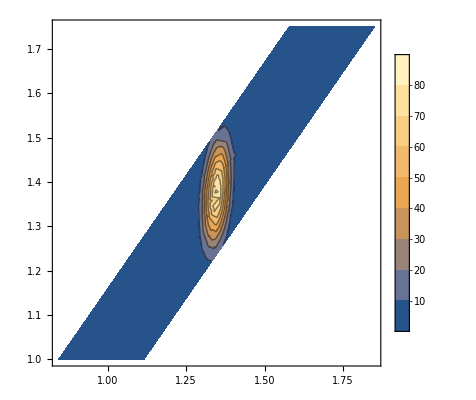

```mathematica
toPlot=49;
ContourPlot[ic0[[toPlot]], {xt,yt}∈Ω[[toPlot]], PlotRange->{0,100}, PlotLegends->Automatic, PerformanceGoal->"Quality"]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,{xt, yt}∈reg, 
Method->{"FiniteElement"}] ;
Print["test"];
Return[(P/.N[[1]])];
]
```

```mathematica
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, meshes}];
```

test

test

test

«46 more identical outputs»

```mathematica
Directory[]
```

/Users/Daniel1

```mathematica
Save["/Users/Daniel1/Research/tissue/mathematica_saved_results/mean_2.wl", solsIc0]
```

```mathematica
solsLoaded = Get["/Users/Daniel1/Research/tissue/mathematica_saved_results/mean_2.wl"]
```

{1}
 |  |  |  |

```mathematica
dv = Table[Derivative[0,1][sol], {sol, solsIc0}];
```

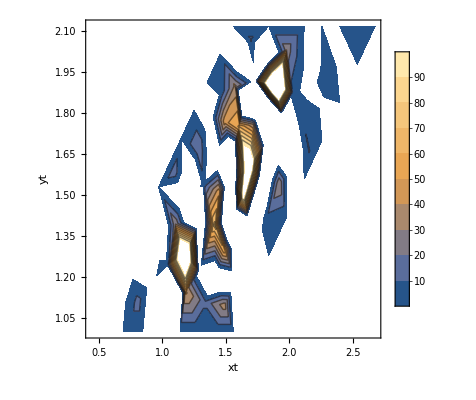

```mathematica
toPlot=1;
ContourPlot[solsIc0[[toPlot]][xt, yt], {xt,yt}∈Ω[[toPlot]], AxesLabel->{xt, yt}, PlotRange->{0, 100}, PlotLegends->Automatic, PerformanceGoal->"Speed"]
```

```mathematica
dv[[1]]
```

$Aborted[]

```mathematica
XIc0 =(MapThread[#1[xt,#2]&,{dv,Table[1, 49]}])*(αArray2/2);
bounds = Transpose[{1/cs-Δx/2, 1/cs+Δx/2}];
```

```mathematica
toPlot=5;
Plot[{XIc0[[toPlot]]}, {xt, bounds[[toPlot,1]], bounds[[toPlot,2]]}, PlotLegends->legend[[1]], PlotRange->{-0.1, 20}]
```

-Graphics-

```mathematica
secondIc0[[6]]
```

1.30024

```mathematica
meansIc0[[6]]^2
```

1.30282

```mathematica
IntegFunc[f_, bound_] :=NIntegrate[f, {xt, bound[[1]], bound[[2]]}]
```

```mathematica
normsIc0 = MapThread[IntegFunc, {XIc0,bounds}]
corrected = MapThread[#1/#2&, {XIc0, normsIc0}];
meansIc0= MapThread[IntegFunc, {corrected*xt,bounds}]
secondIc0 = MapThread[IntegFunc, {corrected*xt*xt,bounds}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0^2;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {0.998671}. NIntegrate obtained 0.999163 and 0.0000552748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00309}. NIntegrate obtained 0.999968 and 0.0000825879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.01545}. NIntegrate obtained 0.999109 and 0.0000836678 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.999163,0.999968,0.999109,0.997032,0.994448,0.987929,0.986231,0.9991,1.00015,0.998703,0.997898,0.993497,0.992058,0.986548,0.998716,1.0003,0.999827,0.999497,0.99538,0.991768,0.986033,0.997144,1.00035,1.00087,0.999807,0.996741,0.994378,0.990282,0.994509,1.00042,1.0008,1.00055,0.998387,0.996328,0.993981,0.990377,0.999578,1.0004,1.00058,0.999195,0.997301,0.995807,0.966036,0.992586,0.996888,0.999408,1.00047,0.999504,0.998585}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {0.998671}. NIntegrate obtained 0.999498 and 0.0000551671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00309}. NIntegrate obtained 1.00685 and 0.0000832532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.01545}. NIntegrate obtained 1.01524 and 0.0000869431 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.999498,1.00685,1.01524,1.02425,1.08457,1.14141,1.19424,0.998995,1.00585,1.01368,1.02207,1.07818,1.12838,1.17997,0.997994,1.004,1.01094,1.01842,1.06895,1.11457,1.16159,0.994976,0.999271,1.00453,1.0104,1.05192,1.09063,1.13123,0.992445,0.995867,1.00027,1.00531,1.04239,1.07803,1.11513,0.989907,0.992721,0.996508,1.00094,1.03465,1.06745,1.1024,0.979632,0.981201,0.983574,0.986528,1.01162,1.03769,1.06637}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00088}. NIntegrate obtained 0.999021 and 0.0000550166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00309}. NIntegrate obtained 1.0138 and 0.0000839353 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.01545}. NIntegrate obtained 1.0308 and 0.000096623 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.999021,1.0138,1.0308,1.04922,1.17675,1.30024,1.42754,0.998016,1.01178,1.02762,1.04475,1.16292,1.27412,1.3936,0.996018,1.00807,1.02208,1.03731,1.14312,1.24315,1.35071,0.99,0.998598,1.00918,1.02104,1.10711,1.19054,1.28157,0.984972,0.991806,1.00064,1.01081,1.08717,1.16302,1.24539,0.979941,0.985551,0.993131,1.00205,1.07118,1.14074,1.21735,0.959698,0.962809,0.96753,0.973413,1.02419,1.0784,1.1397}

{0.0000247622,0.0000533288,0.0000805417,0.000132896,0.000462039,-0.00257999,0.00134388,0.0000247694,0.0000533584,0.0000833231,0.000127792,0.000441931,0.000870194,0.00128045,0.0000247676,0.0000536911,0.0000891222,0.000124852,0.000466901,0.000885756,0.00142274,0.0000226075,0.0000551937,0.0000989858,0.000141757,0.000571288,0.0010654,0.00189481,0.0000247904,0.0000543468,0.0000981412,0.000151069,0.000598311,0.000885697,0.00187025,0.0000248018,0.0000570766,0.000102883,0.000158884,0.000677126,0.00129283,0.0020549,0.0000200639,0.0000542281,0.000111899,0.000175837,0.000814115,0.00159398,0.00255982}

```mathematica
grid = Flatten[Table[{l, a}, {l, λts}, {a, αtvs}], 1];
params
```

{{λt→0.0005,αtv→0.005},{λt→0.0005,αtv→0.01},{λt→0.0005,αtv→0.015},{λt→0.0005,αtv→0.02},{λt→0.0005,αtv→0.05},{λt→0.0005,αtv→0.075},{λt→0.0005,αtv→0.1},{λt→0.001,αtv→0.005},{λt→0.001,αtv→0.01},{λt→0.001,αtv→0.015},{λt→0.001,αtv→0.02},{λt→0.001,αtv→0.05},{λt→0.001,αtv→0.075},{λt→0.001,αtv→0.1},{λt→0.002,αtv→0.005},{λt→0.002,αtv→0.01},{λt→0.002,αtv→0.015},{λt→0.002,αtv→0.02},{λt→0.002,αtv→0.05},{λt→0.002,αtv→0.075},{λt→0.002,αtv→0.1},{λt→0.005,αtv→0.005},{λt→0.005,αtv→0.01},{λt→0.005,αtv→0.015},{λt→0.005,αtv→0.02},{λt→0.005,αtv→0.05},{λt→0.005,αtv→0.075},{λt→0.005,αtv→0.1},{λt→0.0075,αtv→0.005},{λt→0.0075,αtv→0.01},{λt→0.0075,αtv→0.015},{λt→0.0075,αtv→0.02},{λt→0.0075,αtv→0.05},{λt→0.0075,αtv→0.075},{λt→0.0075,αtv→0.1},{λt→0.01,αtv→0.005},{λt→0.01,αtv→0.01},{λt→0.01,αtv→0.015},{λt→0.01,αtv→0.02},{λt→0.01,αtv→0.05},{λt→0.01,αtv→0.075},{λt→0.01,αtv→0.1},{λt→0.02,αtv→0.005},{λt→0.02,αtv→0.01},{λt→0.02,αtv→0.015},{λt→0.02,αtv→0.02},{λt→0.02,αtv→0.05},{λt→0.02,αtv→0.075},{λt→0.02,αtv→0.1}}

```mathematica
normArrayIc0 = ArrayReshape[normsIc0, {7,7}];
varArrayIc0 = ArrayReshape[varsIc0, {7,7}];
meanArrayIc0 = ArrayReshape[meansIc0, {7,7}];
diffArrayIc0 = ArrayReshape[diffIc0,{7,7}];
```

```mathematica
cf[x_]:=Blend[{{0, Red},{ 1,White},{2,Blue}}, x]
xticks = Transpose[{{1, 2, 3, 4, 5, 6, 7}, λts}];
yticks = Transpose[{{1, 2, 3, 4, 5, 6, 7}, αtvs}];
```

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[xt]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, αt}]
Grid[N[Reverse[varArrayIc0],7]]
Grid[N[Reverse[normArrayIc0],7]]
```

-Graphics-

0.0000200639 | 0.0000542281 | 0.000111899 | 0.000175837 | 0.000814115 | 0.00159398 | 0.00255982
0.0000248018 | 0.0000570766 | 0.000102883 | 0.000158884 | 0.000677126 | 0.00129283 | 0.0020549
0.0000247904 | 0.0000543468 | 0.0000981412 | 0.000151069 | 0.000598311 | 0.000885697 | 0.00187025
0.0000226075 | 0.0000551937 | 0.0000989858 | 0.000141757 | 0.000571288 | 0.0010654 | 0.00189481
0.0000247676 | 0.0000536911 | 0.0000891222 | 0.000124852 | 0.000466901 | 0.000885756 | 0.00142274
0.0000247694 | 0.0000533584 | 0.0000833231 | 0.000127792 | 0.000441931 | 0.000870194 | 0.00128045
0.0000247622 | 0.0000533288 | 0.0000805417 | 0.000132896 | 0.000462039 | -0.00257999 | 0.00134388

0.966036 | 0.992586 | 0.996888 | 0.999408 | 1.00047 | 0.999504 | 0.998585
0.990377 | 0.999578 | 1.0004 | 1.00058 | 0.999195 | 0.997301 | 0.995807
0.994509 | 1.00042 | 1.0008 | 1.00055 | 0.998387 | 0.996328 | 0.993981
0.997144 | 1.00035 | 1.00087 | 0.999807 | 0.996741 | 0.994378 | 0.990282
0.998716 | 1.0003 | 0.999827 | 0.999497 | 0.99538 | 0.991768 | 0.986033
0.9991 | 1.00015 | 0.998703 | 0.997898 | 0.993497 | 0.992058 | 0.986548
0.999163 | 0.999968 | 0.999109 | 0.997032 | 0.994448 | 0.987929 | 0.986231

```mathematica
ArrayPlot[ArrayReshape[Table[Blend[{{0, Red},{ 1,White},{2,Blue}}, i],{i,Flatten[meanArrayIc0]}], {7,7}], PlotLegends->{Placed[BarLegend[{cf[#]&,{0, 2}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, αt}]
Grid[N[Reverse[meanArrayIc0],7]]
```

-Graphics-

0.979632 | 0.981201 | 0.983574 | 0.986528 | 1.01162 | 1.03769 | 1.06637
0.989907 | 0.992721 | 0.996508 | 1.00094 | 1.03465 | 1.06745 | 1.1024
0.992445 | 0.995867 | 1.00027 | 1.00531 | 1.04239 | 1.07803 | 1.11513
0.994976 | 0.999271 | 1.00453 | 1.0104 | 1.05192 | 1.09063 | 1.13123
0.997994 | 1.004 | 1.01094 | 1.01842 | 1.06895 | 1.11457 | 1.16159
0.998995 | 1.00585 | 1.01368 | 1.02207 | 1.07818 | 1.12838 | 1.17997
0.999498 | 1.00685 | 1.01524 | 1.02425 | 1.08457 | 1.14141 | 1.19424

```mathematica
Grid[1/Reverse[ArrayReshape[cs, {5, 5}]]]
```

0.723607 | 0.723607 | 0.723607 | 0.723607 | 0.723607
0.816228 | 0.816228 | 0.816228 | 0.816228 | 0.816228
0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298
0.912311 | 0.912311 | 0.912311 | 0.912311 | 0.912311
0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214

```mathematica
Table[(1+Sqrt[1-4l])/2, {l, {0.05, 0.08, 0.1, 0.15,0.2}}]
```

{0.947214,0.912311,0.887298,0.816228,0.723607}

```mathematica
f1 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, %210}]]
```

InterpolatingFunction[…]

```mathematica
f2 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, {1.09,1.01, 0.97,0.86,0.74 }-%210}]]
```

InterpolatingFunction[…]

```mathematica
f3 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, {1.09, 1.01, 0.97, 0.86, 0.74}}]]
```

InterpolatingFunction[…]

```mathematica
f4 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, {1.04, 0.98, 0.94, 0.84, 0.73}}]]
```

InterpolatingFunction[…]

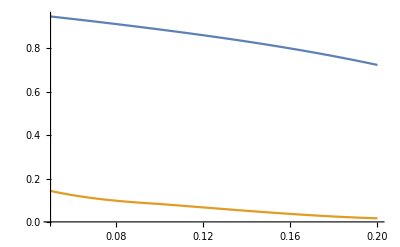

```mathematica
Plot[{f1[x], f2[x]}, {x, 0.05, 0.2}]
```

```mathematica
ArrayPlot[diffArrayIc0, ColorFunction->(Blend[{{ 0,White},{3,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"varScaledToMean2(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
Grid[N[Reverse[diffArrayIc0],4]]
```

-Graphics-

-0.000953224 | 0.00319174 | 0.012927 | 0.0530549 | 0.123451
0.000445732 | 0.0027794 | 0.0112394 | 0.0456622 | 0.104291
0.000416853 | 0.00262419 | 0.0104487 | 0.0420214 | 0.0967817
0.000416854 | 0.00254727 | 0.0103964 | 0.0406542 | 0.0924427
0.000396373 | 0.00254852 | 0.0100826 | 0.0404404 | 0.0913144